```mathematica
vrtx= {1,2,3,4,5,6,7}
```

{1,2,3,4,5,6,7}

```mathematica
dg={1->7,1->3,2->1,2->5,3->6,3->4,4->7,5->1,5->3,5->4,6->5,7->3,7->5}
```

{1->7,1->3,2->1,2->5,3->6,3->4,4->7,5->1,5->3,5->4,6->5,7->3,7->5}

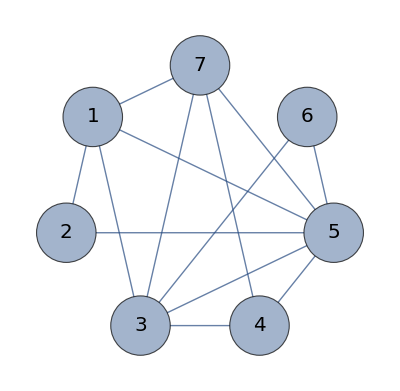

```mathematica
Graph[vrtx,dg,VrtxLabls->Placd["Nam",Cntr],VrtxLablStyl->Dirctiv[Black,Italic,20],GraphLayout->"Circularmbdding",VrtxSiz->0.5,dgShapFunction->GraphlmntData["Arrow","ArrowSiz"->0.05]]
```

```mathematica
vrtx= {1,2,3,4}
```

{1,2,3,4}

```mathematica
dg={1<->2,2<->3,3<->4,4<->1}
```

{1<->2,2<->3,3<->4,4<->1}

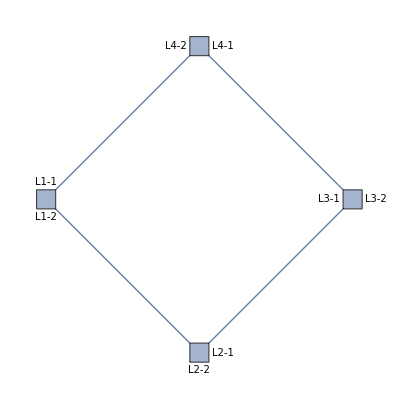

```mathematica
Graph[{Labld[1,Placd[{"L1-1","L1-2"},{Abov,Blow}]],Labld[2,Placd[{"L2-1","L2-2"},{Aftr,Blow}]],Labld[3,Placd[{"L3-1","L3-2"},{Bfor,Aftr}]],Labld[4,Placd[{"L4-1","L4-2"},{Aftr,Bfor}]]},dg,VrtxShapFunction->"Squar",VrtxLablStyl->Dirctiv[Black,Italic,10],GraphLayout->"Circularmbdding",VrtxSiz->0.1]
```


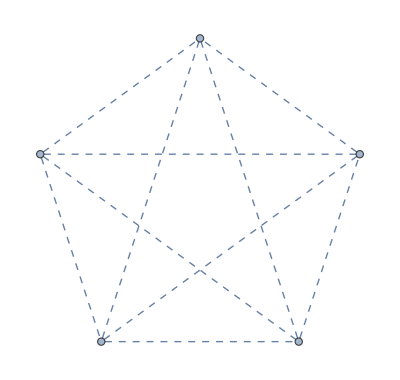
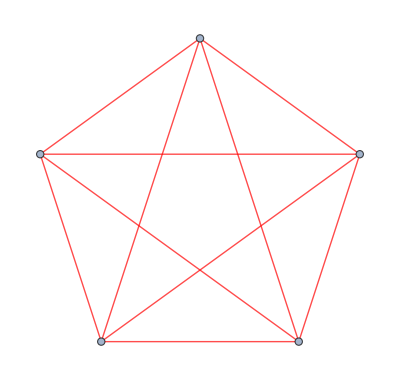

```mathematica
Tabl[CompltGraph[5,dgStyl->styl],{styl,{Thick,Dashd,Rd}}]
```

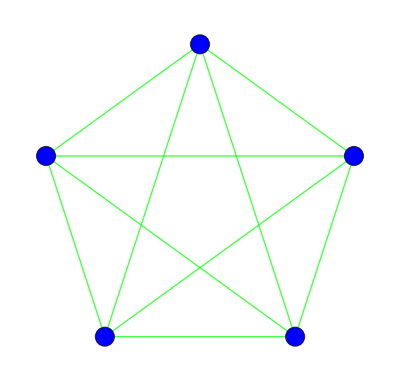
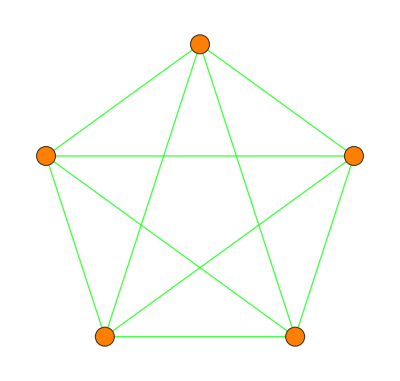
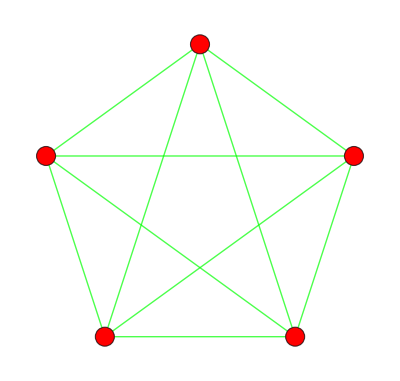

```mathematica
Tabl[CompltGraph[5,dgStyl->Grn,VrtxSiz->Small,VrtxStyl->styl],{styl,{Blu,Orang,Rd}}]
```

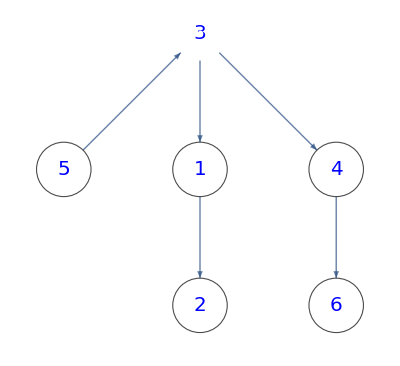

Graph::nonopt: Options expected (instead of Null) beyond position 2 in Graph[{1->2,3->1,3->4,4->6,5->3},VertexSize→Large,Null,VertexStyle→GrayLevel[1],VertexLabels→Placed[Name,Center],VertexLabelStyle→Directive[RGBColor[0, 0, 1],Italic,20],GraphLayout→LayeredEmbedding]. An option must be a rule or a list of rules.

```mathematica
Graph[{1->2,3->1,3->4,4->6,5->3},VrtxSiz->Larg,VrtxShap->{3->Import["xamplData/turtl.jpg"]},VrtxStyl->Whit,VrtxLabls->Placd["Nam",Cntr],VrtxLablStyl->Dirctiv[Blu,Italic,20],GraphLayout->"Layrdmbdding"]
```

```mathematica
Graph[{1->2,3->1,3->4,4->6,5->3},VrtxSiz->Larg,Null,VrtxStyl->GrayLevel[1],VrtxLabls->Placd["Nam",Cntr],VrtxLablStyl->Dirctiv[RGBColor[0, 0, 1],Italic,20],GraphLayout->"Layrdmbdding"]
```

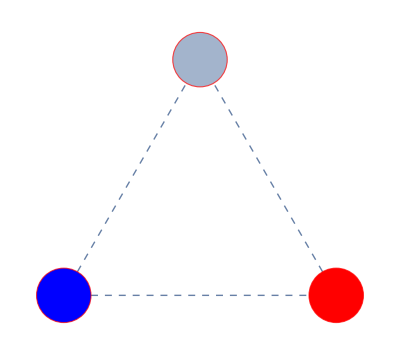
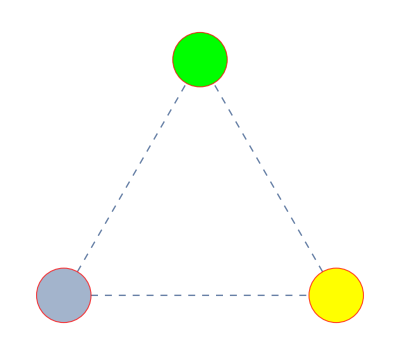
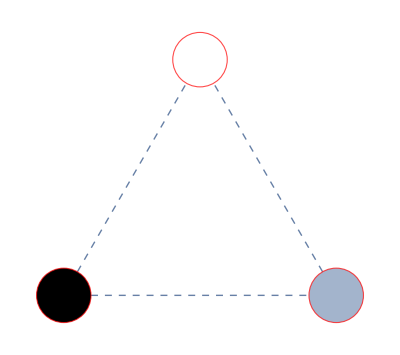

```mathematica
Tabl[Graph[{1<->2,2<->3,3<->1},VrtxStyl->styl ,VrtxSiz->0.2,BasStyl->dgForm[Rd],dgStyl->Dashd],{styl,{{1->Blu,2->Rd},{2->Yllow,3->Grn},{1->Black,3->Whit}}}]
```

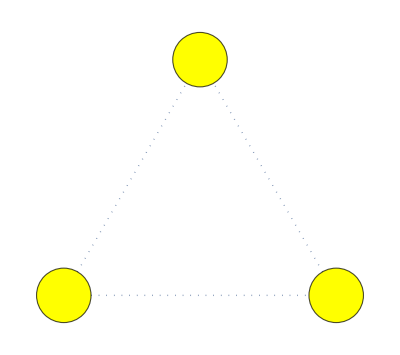
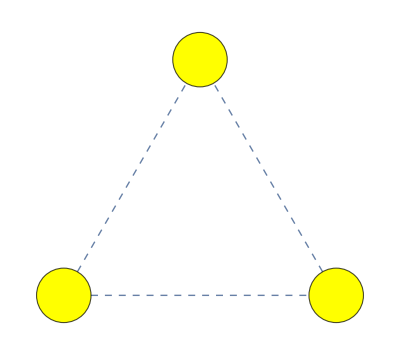
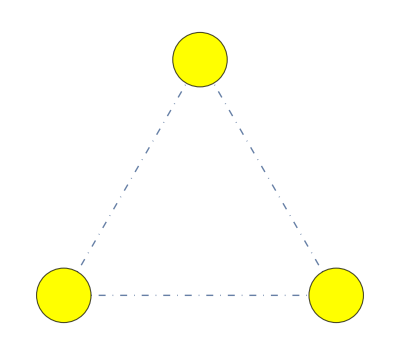

```mathematica
Tabl[Graph[{1<->2,2<->3,3<->1},VrtxStyl->Yllow,BasStyl->dgForm[styl],dgStyl->styl,VrtxSiz->0.2],{styl,{Dottd,Dashd,DotDashd}}]
```

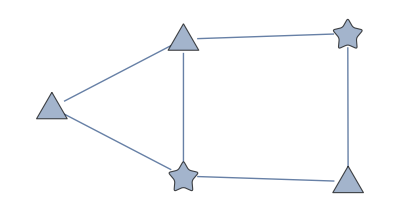

```mathematica
Graph[{1,2,3,4,5},{1<->2,1<->4,2<->3,2<->5,3<->5,3<->4},VrtxShapFunction->{ _?vnQ->
"ConcavPntagon", _?OddQ->"Triangl"},VrtxSiz->0.2]
```

```mathematica
Graph[{1,2,3,4,5},VrtxShapFunction->{vnQ->"ConcavPntagon",OddQ->"Triangl"},VrtxSiz->0.2]
```

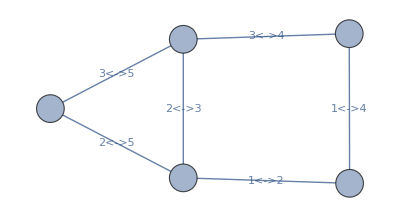

```mathematica
Graph[{1,2,3,4,5},{Labld[1<->2,"1<->2"],Labld[1<->4,"1<->4"],Labld[2<->3,"2<->3"],Labld[2<->5,"2<->5"],Labld[3<->5,"3<->5"],Labld[3<->4,"3<->4"]},VrtxShapFunction->"Circl",VrtxSiz->0.2]
```

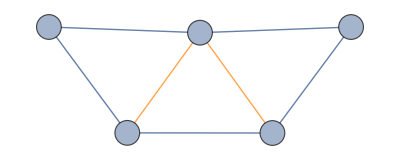

```mathematica
Graph[{1->2,2->3,3->1,3->4,4->1, 4->5, 5->3 },VrtxSiz->Mdium,VrtxLabls->Placd["Nam", Cntr], dgStyl->{3->_->Orang},dgShapFunction->GraphlmntData["Arrow","ArrowSiz"->0.05]]
```

```mathematica
DirctdGraph[CompltGraph[5, VrtxSiz-> Larg, VrtxLabls->Placd["Nam", Cntr], VrtxLablStyl->Dirctiv[Italic,20],dgShapFunction->GraphlmntData["Arrow","ArrowSiz"->0.05],GraphHighlightStyl->"Dashd",GraphHighlight-> {1,1->2,1->3,1->4,1->5}], "Acyclic"]
```

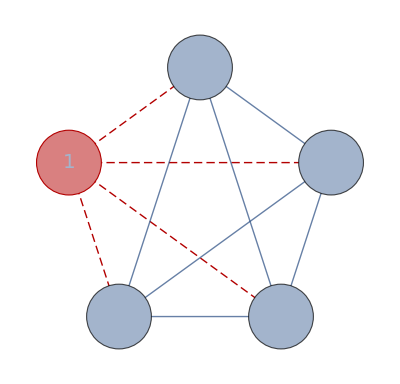

-Graphics-

```mathematica
HighlightGraph[DirctdGraph[CompltGraph[5, VrtxSiz-> Larg, VrtxLabls->Placd["Nam", Cntr], VrtxLablStyl->Dirctiv[Italic,20],dgShapFunction->GraphlmntData["Arrow","ArrowSiz"->0.05]], "Acyclic"],{1,1->2,1->3,1->4,1->5}, GraphHighlightStyl->"Dashd"]
```

-Graphics-

```mathematica
faf
```

faf

```mathematica
Graph[{1->2,2->3,3->1,3->4,4->1, 4->5, 5->3 },VrtxSiz->Mdium,VrtxLabls->Placd["Nam", Cntr],GraphHighlightStyl->"Dashd", dgStyl->{3->_->Orang},dgShapFunction->GraphlmntData["Arrow","ArrowSiz"->0.05]]
```

-Graphics-

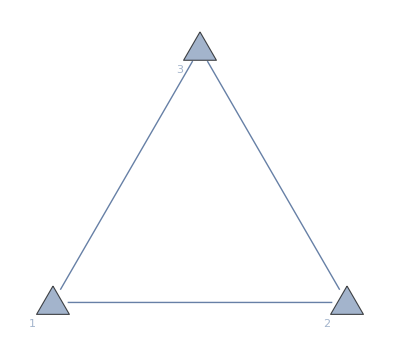

```mathematica
Graph[{Labld[1,Placd[{"1","1"},{Cntr,{Bfor,Blow}}]],Labld[2,Placd[{"2","2"},{Cntr,{Bfor,Blow}}]],Labld[3,Placd[{"3","3"},{Cntr,{Bfor,Blow}}]]},{1<->2,2<->3,3<->1},VrtxShapFunction->{ "Triangl"},VrtxSiz->0.1]
```

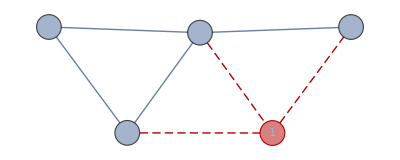

```mathematica
HighlightGraph[Graph[{1->2,2->3,3->1,3->4,4->1, 4->5, 5->3 },VrtxSiz->Mdium,VrtxLabls->Placd["Nam", Cntr],GraphHighlightStyl->"Dashd", dgShapFunction->GraphlmntData["Arrow","ArrowSiz"->0.05]],{1,1->2,3->1,4->1}, GraphHighlightStyl->"Dashd"]
```

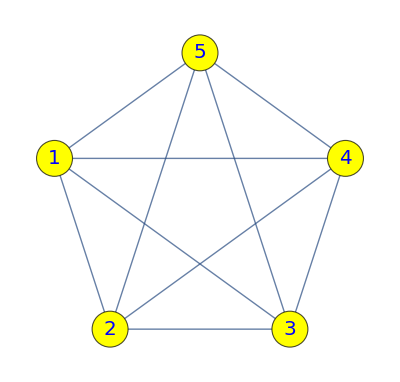

```mathematica
CompltGraph[5, VrtxSiz->0.2,dgStyl->Dirctiv["Dashd"],VrtxStyl->Yllow, VrtxLabls->Placd["Nam", Cntr], VrtxLablStyl->Dirctiv[Blu,Italic,20]]
```

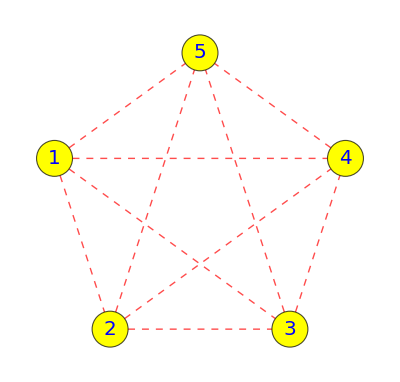

```mathematica
CompltGraph[5,VrtxSiz->0.2,VrtxLablStyl->Dirctiv[Italic,20,Blu],VrtxLabls->Placd["Nam",Cntr],VrtxStyl->Yllow,dgStyl->Dirctiv[Rd,Dashd]]
```

```mathematica
Graph[{1,2,3,4,5},{1<->2,1<->4,2<->3,2<->5,3<->5,3<->4},VrtxShapFunction->{ _?vnQ->
"ConcavPntagon", _?OddQ->"Triangl"},VrtxSiz->0.2]
```

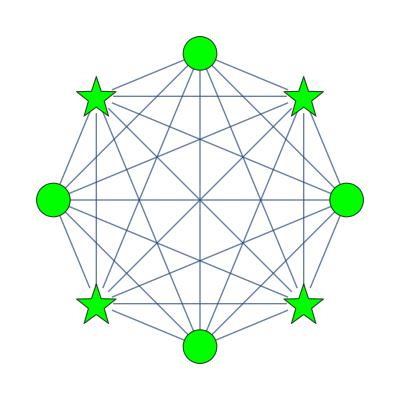

```mathematica
CompltGraph[8, VrtxSiz-> 0.3,VrtxStyl->Grn, VrtxLablStyl->Dirctiv[Italic,20],VrtxShapFunction->{ _?vnQ->"Circl", _?OddQ->"Star"}]
```

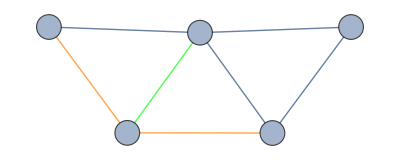

```mathematica
Graph[{1->2,2->3,3->1,3->4,4->1, 4->5, 5->3 },VrtxSiz->Mdium,VrtxLabls->Placd["Nam", Cntr], dgStyl->{4->_->Orang,3->4->Grn},dgShapFunction->GraphlmntData["Arrow","ArrowSiz"->0.05]]
```

```mathematica
CompltGraph
```

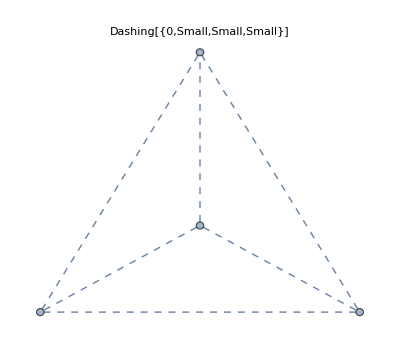

```mathematica
CompltGraph[4,dgStyl->Dashd,PlotLabl->DotDashd]
```

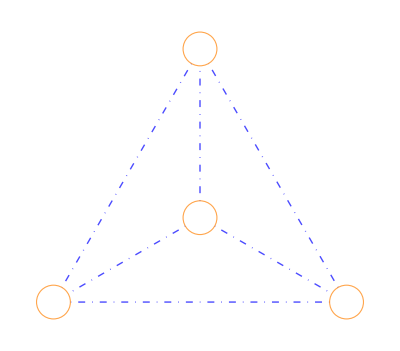

7

13

{{1,7},{1,3},{2,1},{2,5},{3,6},{3,4},{4,7},{5,1},{5,3},{5,4},{6,5},{7,3},{7,5}}

{1,2,3,4,5,6,7}

```mathematica
CompltGraph[4,VrtxStyl->Whit,VrtxSiz->Mdium,BasStyl->dgForm[Dirctiv[Dashd,Orang]],dgStyl->Dirctiv[DotDashd,Blu]]
```

```mathematica
filePath=StringJoin[{NotebookDirectory[],"input.txt"}];
fileStream=OpenRead[filePath];
I1=Read[fileStream,{Word,Number}][[2]]
U1=Read[fileStream,{Word,Number}][[2]]
edgList=ReadList[fileStream,Expression,U1]
bList=ReadList[fileStream,{Word,Number},I1]
close[fileStream];
```

7

13

{{1,7},{1,3},{2,1},{2,5},{3,6},{3,4},{4,7},{5,1},{5,3},{5,4},{6,5},{7,3},{7,5}}

{{/*b_1*/,7},{/*b_2*/,4},{/*b_3*/,-1},{/*b_4*/,-7},{/*b_5*/,-2},{/*b_6*/,-1},{/*b_7*/,0}}

```mathematica
filePath=StringJoin[{NotebookDirectory[],"input.txt"}];
fileStream=OpenRead[filePath];
countVertex=Read[fileStream,{Word,Number}][[2]];
setVertex=Array[#&,countVertex];
countEdge=Read[fileStream,{Word,Number}][[2]];
Edges=ReadList[fileStream,Expression,countEdge];
setEdge=Table[Edges[[i,1]]->Edges[[i,2]],{i,countEdge}];vectorB=Array[0&,countVertex];
listInput=ReadList[fileStream,String];
For[i=1,i≤countVertex,i++,vectorB[[i]]=ToExpression[StringSplit[listInput[[i]],{"a","_","/*","*/"}]][[2]]];Close[fileStream];
```